```mathematica
Helver Jussef López Abril
Michael Velasquez Rico
```

Metodo de Newton-raphson

```mathematica
FindRoot[x Exp[x]-2,{x,1.5}]
```

{x→0.852606}

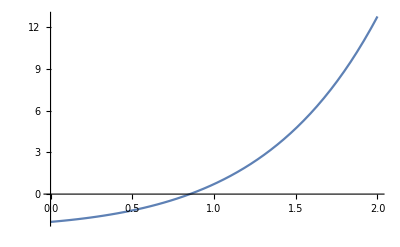

```mathematica
Plot[x Exp[x]-2,{x,0,2}]
```

```mathematica
Subscript[x, 0]=1.5;
f[x_]:=x  ⅇ^x-2
For[n=0,n≤3,n++,Subscript[x, n+1]=Subscript[x, n]-f[Subscript[x, n]]/f'[Subscript[x, n]]];
  Print ["La solucion aproximada es =  ", N[Subscript[x, 3]_,20]]; Print [ "error estimado = " ,N[Abs[(Subscript[x, 3]-Subscript[x, 2])/Subscript[x, 3]],2]]
```

La solucion aproximada es =  0.85349_Null

error estimado = 0.0391186